Practical-2: Secant Method
Name: Devansh Tyagi
Roll No: 20221416
B.Sc. (Hons.) Computer Science

Secant Method: For Given Parameters
Ques-1

x0= 0

x1= 1

Nmax= 100

epsilon= 0.001

f(x):=Cos[x]

1th iteration value is: 2.17534

estimate error is: 1.17534

2th iteration value is: 1.57278

estimate error is: 0.602559

3th iteration value is: 1.57067

estimate error is: 0.00211435

Return[1.5708]

root is: 1.5708

Estimate error is: 0.000126873

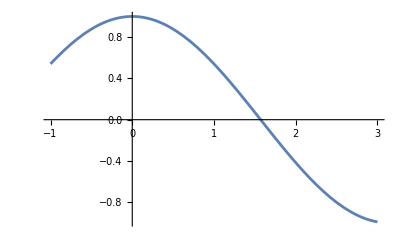

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x];
Print["f(x):=", f[x]];
For[i=1, i<=Nmax, i++,
	x2 = N[x1- (f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1) - (f[x]/.x->x0))];
	If[Abs[x1-x2] < eps, Return[x2], x0 = x1; x1=x2];
	Print[i, "th iteration value is: ", x2];
	Print["estimate error is: ", Abs[x1-x0]]];
Print["root is: ", x2];
Print["Estimate error is: ", Abs[x2-x1]];
Plot[f[x], {x, -1, 3}]
```

Ques-2

x0= 1

x1= 2

Nmax= 100

epsilon= 0.0001

f(x):=ⅇ^x x-Cos[x]

1th iteration value is: 0.832673

estimate error is: 1.16733

2th iteration value is: 0.728779

estimate error is: 0.103894

3th iteration value is: 0.562401

estimate error is: 0.166377

4th iteration value is: 0.524782

estimate error is: 0.0376189

5th iteration value is: 0.518014

estimate error is: 0.00676874

6th iteration value is: 0.517759

estimate error is: 0.0002547

Return[0.517757]

root is: 0.517757

Estimate error is: 1.50138×10^-6

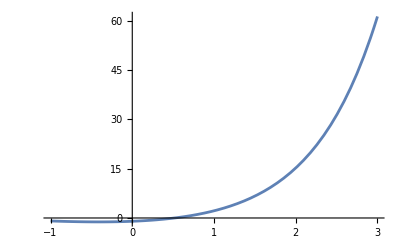

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := x*ⅇ^x - Cos[x];
Print["f(x):=", f[x]];
For[i=1, i<=Nmax, i++,
	x2 = N[x1- (f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1) - (f[x]/.x->x0))];
	If[Abs[x1-x2] < eps, Return[x2], x0 = x1; x1=x2];
	Print[i, "th iteration value is: ", x2];
	Print["estimate error is: ", Abs[x1-x0]]];
Print["root is: ", x2];
Print["Estimate error is: ", Abs[x2-x1]];
Plot[f[x], {x, -1, 3}]
```

Ques-3

x0= 1

x1= 2

Nmax= 100

epsilon= 0.001

f(x):=3 x+Log[x]

1th iteration value is: 0.187685

estimate error is: 1.81232

2th iteration value is: 0.445475

estimate error is: 0.25779

3th iteration value is: 0.362395

estimate error is: 0.08308

4th iteration value is: 0.349237

estimate error is: 0.0131578

Return[0.349976]

root is: 0.349976

Estimate error is: 0.000738941

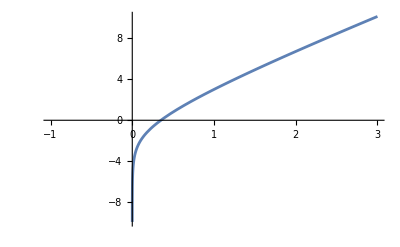

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := 3x + Log[x];
Print["f(x):=", f[x]];
For[i=1, i<=Nmax, i++,
	x2 = N[x1- (f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1) - (f[x]/.x->x0))];
	If[Abs[x1-x2] < eps, Return[x2], x0 = x1; x1=x2];
	Print[i, "th iteration value is: ", x2];
	Print["estimate error is: ", Abs[x1-x0]]];
Print["root is: ", x2];
Print["Estimate error is: ", Abs[x2-x1]];
Plot[f[x], {x, -1, 3}]
```

x0= 1

x1= 2

Nmax= 100

epsilon= 0.001

f(x):=-4-3 x+x^3

1th iteration value is: 2.5

estimate error is: 0.5

2th iteration value is: 2.16327

estimate error is: 0.336735

3th iteration value is: 2.19073

estimate error is: 0.0274652

4th iteration value is: 2.19592

estimate error is: 0.0051897

Return[2.19582]

root is: 2.19582

Estimate error is: 0.0000970961

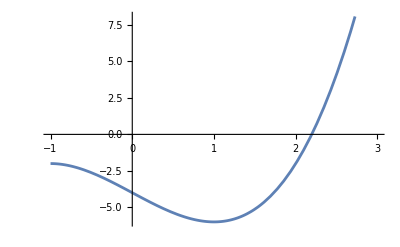

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := x^3-3*x-4;
Print["f(x):=", f[x]];
For[i=1, i<=Nmax, i++,
	x2 = N[x1- (f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1) - (f[x]/.x->x0))];
	If[Abs[x1-x2] < eps, Return[x2], x0 = x1; x1=x2];
	Print[i, "th iteration value is: ", x2];
	Print["estimate error is: ", Abs[x1-x0]]];
Print["root is: ", x2];
Print["Estimate error is: ", Abs[x2-x1]];
Plot[f[x], {x, -1, 3}]
```